```mathematica
ThermodynamicData[][[1]]//InputForm
```

"Acetone"

```mathematica
subs=ThermodynamicData[]
```

{Acetone,Air,Ammonia,Argon,Benzene,Butane,Butene,CarbonDioxide,CarbonMonoxide,CarbonylSulfide,CisButene,Cyclohexane,Cyclopentane,Cyclopropane,Decamethylcyclopentasiloxane,Decamethyltetrasiloxane,Decane,Deuterium,DiethylEther,DimethylCarbonate,DimethylEther,Dodecamethylcyclohexasiloxane,Dodecamethylpentasiloxane,Dodecane,Ethane,Ethanol,Ethylbenzene,Ethylene,Fluorine,HeavyWater,Helium,Heptane,Hexamethyldisiloxane,Hexane,Hydrogen,HydrogenChloride,HydrogenSulfide,Isobutane,Isobutene,Isohexane,Isooctane,Isopentane,Krypton,Methane,Methanol,Methylcyclohexane,MethylLinoleate,MethylLinolenate,MethylOleate,MethylPalmitate,MethylStearate,MXylene,Neon,Neopentane,Nitrogen,NitrogenTrifluoride,NitrousOxide,Nonane,Novec649,Octamethylcyclotetrasiloxane,Octamethyltrisiloxane,Octane,Orthohydrogen,Oxygen,OXylene,Parahydrogen,Pentane,Perfluorobutane,Perfluoropentane,Propane,Propylcyclohexane,Propylene,Propyne,PXylene,R11,R113,R114,R115,R116,R12,R1216,R123,R1233zd,R1234yf,R1234ze,R124,R125,R13,R134a,R14,R141b,R142b,R143a,R152a,R161,R21,R218,R22,R227ea,R23,R236ea,R236fa,R245ca,R245fa,R32,R365mfc,R40,R41,RC318,RE143a,RE245cb2,RE245fa2,RE347mcc,SulfurDioxide,SulfurHexafluoride,Tetradecamethylhexasiloxane,Toluene,TransButene,Trifluoroiodomethane,Undecane,Water,Xenon}

```mathematica
Length[points]
```

122

```mathematica
points={ThermodynamicData[#,"TriplePointTemperature"]/Quantity[1,"Kelvins"],
ThermodynamicData[#,"TriplePointPressure"]/Quantity[1,"Atmospheres"]}&/@subs
```

```mathematica
?Select
```

```mathematica
Select[points,#[[1]]>100&&#[[2]]>.007&]
```

{{195.495,0.0601135},{278.674,0.0472243},{216.592,5.11177},{279.47,0.0517168},{277.06,0.0219738},{187.7,0.22946},{115.775,0.725685},{256.6,0.349371},{182.33,0.866913},{236.93,0.0184653},{173.75,0.0218406},{173.1,0.25739},{220.,0.310881},{172.52,0.0287589},{161.34,0.0106084},{239.,0.024456},{131.4,0.00888231},{233.35,0.192065},{240.,0.644954},{250.,0.273082},{250.,0.0816383},{250.,0.0673575},{197.7,0.0163829},{223.555,2.28403},{161.405,0.807007}}

```mathematica
ListLogLogPlot[points->subs,ImageSize->Large,Frame->True,FrameLabel->{"T (K)", "P (atm)"},PlotLabel->"Triple points of 12 substances",PlotRange->{{180,280},{.055,All}}]
```

-Graphics-

```mathematica
ThermodynamicData["Neopentane",#]&/@{"TriplePointPressure","TriplePointTemperature"}
```

{35400. Pa,256.6 K}

```mathematica
ThermodynamicData["RE143a",#]&/@{"TriplePointPressure","TriplePointTemperature"}
```

{65350. Pa,240. K}

```mathematica
ListLogLogPlot[points->subs,ImageSize->Large,Frame->True,FrameLabel->{"T (K)", "P (atm)"},PlotLabel->"Triple points of 122 substances"]
```

-Graphics-

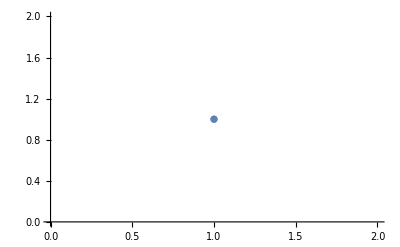

```mathematica
ListPlot[{{Quantity[1,"Kelvins"],Quantity[1,"Pascals"]}}]
```